# Vizualizacija filozofskih konceptov

## Donald Davidson: Raziskave o resnici in interpretaciji

### Anomalizem mentalnega (prevedljivost primerkov)

Davidson je v filozofiji duha znan po svojem zagovoru anomalizma mentalnega v kombinaciji z vzročnim determinizmom. Pozicija vključuje tri temeljne predpostavke, ki so pred Davidsonom običajno veljale za medsebojno izključujoče:
1. Vzročna interakcija med mentalnimi in fizikalnimi dogodki (vsaj nekaterimi)
2. Nomološka narava vzročnosti (za vsako vzročno zvezo nujno obstaja strog zakon)
3. Anomalizem mentalnega (deterministični zakoni, ki bi napovedovali mentalne dogodke ne obstajajo)

```mathematica
(*Oblikovanje objektov*)
MentalniDogodki =Style[Cylinder[{{0,0,1},{0,0,1.04}},Sqrt[2]],Opacity[0.6,Yellow]];
NapisMent=Text[Style["Mentalni dogodki", 14, Black ], {0,0,1}];
NapisFiz=Text[Style["Fizikalni dogodki", 14, Black ], {0,0,-1}];
FizikalniDogodki=Style[Cylinder[{{0,0,-1.04},{0,0,-1}},Sqrt[2]],Opacity[0.6,Blue]];
(*Ti "čudni" koeficienti so tu samo za videz naključne razporeditve*)
Puscice=Table[Arrow[{{Cos[21.72 t],Sin[27.7t],1},{ 1.11 Cos[3 t],0.88 Sin[2 t],-1}}],{t,0,2 Pi -0.1,Pi/4}];
(*Izrisovanje*)
Graphics3D[{MentalniDogodki,FizikalniDogodki,Puscice, NapisMent,NapisFiz},ImageSize->Large]
```

-Graphics3D-

Glavna poanta, ki je relevantna za projektiranje je ideja prevedljivosti primerkov brez prevedljivosti območij. Davidsonova teorija se izteče v ločeni sferi, kjer mentalno ne more biti zreducirano na fizikalno, lahko pa je zreduciran katerikoli posamezen primer mentalnega stanja. Argument stoji na tezi, da mentalna stanja niso pripisljiva ali sploh smiselna, če že ne delujemo pod predpostavko drugih (preteklih in / ali prihodnjih mentalnih stanj, npr. pričakujem, da se me bo nekdo razveselil, ker ima do mene določeno pozitivno čustveno naklonjenost). Hkrati s tem pa trdimo, da se vsaka takšna situacija v trenutku, da izraziti kot neko fizikalno stanje (vzburjenja na sinapsah, ta in ta kemična reakcija...). S tem mu je uspelo združiti tri teze, ki sem jih naštel zgoraj.

## Gilles Deleuze

### Uvod

Intelektualno ozračje poznega 20. stoletja definira miselni tok, ki ga pogosto imenujemo postmodernizem. Čeravno je bila misel v tem času gotovo pluralna in nikakor poenotena pa se splača obdržati v mislih osnovno temo skepticizma do ambicioznih, vseobsežnih teorij, jasnih, ostrih klasifikacij in predalčkanj ter pretenzij o dosopu do stvari kot so v “resnici”. Eden izmed ključnih mislecev iz tega obdobja je Giles Deleuze, posebej dobro znan iz svojega poznejšega ustvarjalega obdobja s Felixom Guattarijem. 
*Opozorilo: vse kar sledi od tu naprej je moj poskus vizualizacije in rekonstrukcije avtorjevih idej iz Razlike in ponavljanja, ki jih iskreno še ne razumem dovolj dobro. Se opravičujem za površnosti, napake in poenostovitve, ki bodo neizogibno sledile.

### Singularnosti

Deleuze ponuja nov način razmišljanja o tem, kar je tradicionalno definirano kot objekti. Namesto stagnante, fiksirane identitete lahko nek pojav definiramo preko odnosov in razmerij. Pri tem identitete ne zavračamo, ampak jo razumemo kot končni produkt ne pa temeljno danost. Ta koncept bomo poenostavljeno pokazali s točkami.

Točke so elementi, ki se med sabo ne razlikujejo po ničemer razen po svoji legi . V našem primeru je ta lega definirana le preko drugih točk . To pomeni, da že vnos ene same točke popolnoma spremeni lastnosti vsake druge točke v sistemu . To bo nekoliko bolj vidno na manjšem sistemu točk .

```mathematica
noveTocke=Table[{RandomReal[{-3,3}],RandomReal[{-5,5}]}, 2];
ListPlot[noveTocke, Axes -> False, PlotMarkers->Automatic]
```

```mathematica
dodTocke = Join[{{RandomReal[{-1,1}],RandomReal[{-5,5}]}},noveTocke];

SpremeniKoord=SessionSubmit[ScheduledTask[dodTocke[[1]] ={RandomReal[{-3,3}],RandomReal[{-5,5}]},{Quantity[5, "Seconds"],10}]];

Dynamic[
ListPlot[dodTocke, Axes -> False, PlotMarkers->Automatic]
]
```

Zakaj lahko govorimo o spremembi vseh lastnosti, ko pa začetni dve točki nista spremenili svojega položaja? To vprašanje je že v izhodišču narobe. Točki gotovo sta spremenili svoj položaj glede na prej postavljeni standard lokacije . Ne le, da je njuna lokacija sedaj definirana z relacijo do ene točke več, ampak je to relacijo do točke več pridobila tudi druga točka iz začetnega para . Z lokacijo smo točkam sedaj sicer pripisali identiteto, vendar je iz dosedanjega razmisleka jasno, da so bile vse interakcije in spremembe v sistemu pogojene z igro razmerji, medtem ko je identite le češnja na vrhu, ki pride kot ontološko zadnja .

*Namenom smo odstranili številske osi, saj bomo poskušali o točkah razmišljati le glede na njihove medsebojne odnose . (S tem mislim njihovo lego relativno ena na drugo, ne pa na absolutni standard lokacije, ki ga zagotavlja koordinatni sistem .)

```mathematica
tocke=Join[
Table[{RandomInteger[{-4, 4}],RandomInteger[{-10, 10}]}, 11], 
{Missing}, Table[{RandomInteger[{5, 9}],RandomInteger[{-10, 10}]}, 5], 
{Missing}] ;
```

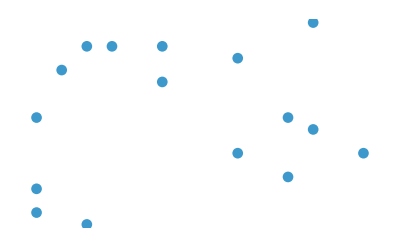

```mathematica
ListPlot[tocke, Axes -> False, PlotMarkers->Automatic]
```

Dane točke lahko seveda poskusimo fiksirati in jim vsiliti določeno obliko, ampak ta oblika pride kasneje kot točke, je arbitrarna, (lahko drugačen vrstni red, lahko s krivo črto...) in ne more biti obravnavana kot priviligirana v primerjavi s točko.

```mathematica
SpremeniVzorec=SessionSubmit[ScheduledTask[tocke = RandomSample[tocke],{Quantity[1, "Seconds"],15}]];
SpremeniVzorec[tocke];
Dynamic[ListLinePlot[tocke, Axes -> False, PlotMarkers->Automatic]]
```

Še posebno mikavno so totalizirajoče oblike, ki vežejo vse elemente danega sistema. Tovrstne oblike se pojavljajo na skoraj vsaki stopnji zgodovine ontološke misli pa naj bo to v obiliki kozmosa, platonskega / novoplatonskega dobrega / enega, enotnosti v Bogu, duhu, umu...

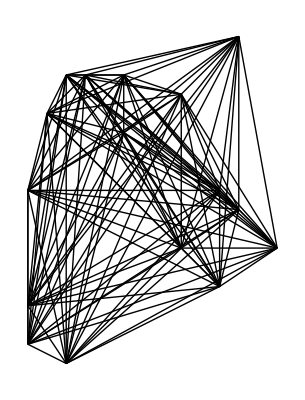

```mathematica
(*izločim prekinitve iz seznama (v tockah sta dva elementa missing)*)
tockeBrezLuknenj=List[];
For[i=1, i<=Length[tocke],i++,
If[Length[tocke[[i]]]==2, AppendTo[tockeBrezLuknenj, tocke[[i]]],1]
]
(*Zdaj narišem*)
totalniVzorec=Map[Line,Subsets[tockeBrezLuknenj,{2}]];
Graphics[totalniVzorec]
```

In ta odgovor se še danes zdi prepričjiv. Izrazi namreč prav vse možne zveze hkrati in enkrat za vselej. Pa vendar ta odgovor ni zadosten. Predpostavlja namreč enakovrednost vseh zvez in hkratno dosopnost vseh točk. Nimamo pa nobenega garanta, da so vse točke v sistemu hkrati na voljo ena druga niti, da ne morejo vzpostavljati meta zvez (med manjšimi sistemi razmerij), da nosijo enako težo na pram ena drugi. Zadnji ugovor bomo pustili ob strani, saj ne uspe zavrniti pozicije, ki jo kritiziramo. Zlahka bi namreč zgornji skici dodali hipotetične “koeficiente obtežitve” za vsako zvezo in se mu popoloma izognili. Prva dva ugovora pa po mojem predstavljata veliko močnejše kritično izhodišče.

Za začetek si poglejmo idejo meta zvez .

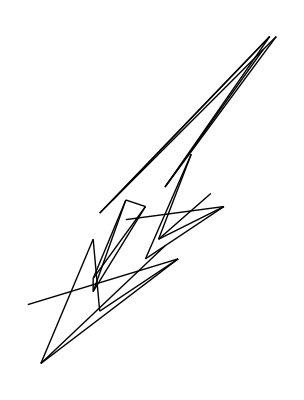

```mathematica
NarediSistem[zacetek_, tocke_, korak_, konec_]:=(*Proizvede tabelo točk za sistem*)Subsets[Take[tocke,{zacetek, konec, korak}], {2}];

Narisi[sistem_]:=(*Nariše totaliziran sistem*)Graphics[ Map[Line, sistem]];

PrestaviVsakX[sistem_,premik_]:=(*prestavi vse točke v sistemu po x osi za premik*)Map[# +{premik,0}&,  sistem];

sistem1=Narisi[NarediSistem[1, tockeBrezLuknenj, 4, 16]];
sistem2=Narisi[PrestaviVsakX[NarediSistem[2, tockeBrezLuknenj, 4, 16],10]];
sistem3 =Narisi[PrestaviVsakX[NarediSistem[3, tockeBrezLuknenj, 4, 16],25]];
sistem4=Narisi[PrestaviVsakX[NarediSistem[4, tockeBrezLuknenj, 4, 16],-10]];
Show[sistem1, sistem2, sistem3, sistem4]
```

Povsem smiselna je teza, da so določene interakcije mogoče šele med sistemi višjega reda oz. da vzpostavljanje razmerij omogoča pojav novih razmerij (in seveda tudi da so obstoječa razmerja pogojena s predhodnimi razmerji, ki so jih omogočila). Za nekoliko banalen primer, je jasno, da se odpre neko polje novih možnih razmerij, v trenutku, ko je iz delov sestavljeno kolo. (na primer prometna nesreča, v katero je kolo lahko vpleteno bistveno drugače kot recimo en samostojen člen verige).  Ta nova možna razmerja lahko spet vplivajo na začetne oblike z nadaljnim povezovanjem, kjer bodisi tvorijo še en meta nivo nad trenutnim, ponudijo rekonfiguracijo trenutnega nivoja (na animaciji spodaj) ali pa razpad določenih zvez trenutnega nivoja na nižjo stopnjo zvez.

```mathematica
SpremeniVzorceSistemov=SessionSubmit[ScheduledTask[tockeBrezLuknenj = RandomSample[tockeBrezLuknenj];
sistem1=Narisi[NarediSistem[1, tockeBrezLuknenj, 4, 16]];
sistem2=Narisi[NarediSistem[2, tockeBrezLuknenj, 4, 16]];
sistem3 =Narisi[NarediSistem[3, tockeBrezLuknenj, 4, 16]];
sistem4=Narisi[NarediSistem[4, tockeBrezLuknenj, 4, 16]];
,{Quantity[2, "Seconds"],15}]];
Dynamic[Show[sistem1, sistem2, sistem3, sistem4]]
```

#### Aplikacija v oblaku

Še enkrat je vredno poudariti, da črte v tem primeru ne nakazujejo fiksiranih oblik, ampak še vedno zgolj točkovna razmerja. Črte zgolj izpostavijo, katere točke so si med sabo v danem trenutku dostopne. Skozi to dostopnost se lahko potem seveda takoj vzpostavijo nove nadgrajujoče zveze, vendor tega nisem znal lepo pokazati, zato spodnja animacija prikazuje predvsem razpad in rekonfiguracijo.

```mathematica
Rekonfiguracije :=DynamicModule[
(*spremenljivke*)
{tockeZaPrikaz,zacetneZveze,zacetneZvezeSistemi},
Manipulate[
(*To kar se mora izvajati*)
ResourceFunction["JoinTo"][zacetneZvezeSistemi[[2]],{ResourceFunction["Pop"][zacetneZvezeSistemi[[1]],{2}]}];
ResourceFunction["JoinTo"][zacetneZvezeSistemi[[1]],{ResourceFunction["Pop"][zacetneZvezeSistemi[[3]],{2}]}];
ResourceFunction["JoinTo"][zacetneZvezeSistemi[[3]],{ResourceFunction["Pop"][zacetneZvezeSistemi[[2]],{2}]}];
sistemZaSpremembo=RandomInteger[{1,3}];
zacetneZvezeSistemi[[sistemZaSpremembo]]=PrestaviVsakX[zacetneZvezeSistemi[[sistemZaSpremembo]],RandomReal[{-50,50}]];

(*Prikaz*)
Show[NarisiBarvno[zacetneZvezeSistemi[[1]],Red],NarisiBarvno[zacetneZvezeSistemi[[2]],Blue],NarisiBarvno[zacetneZvezeSistemi[[3]],Green]],

(*Kontrole*)
{step,1,20,1,ControlType->None,AnimationRepetitions->2,AnimationRunning->True,AnimationRate->2},

(*To,kar naj funkcija sproti preverja*)
TrackedSymbols->{step},

(*Začetek (izvede se samo prvič)*)
Initialization:>{
(*Funkcije*)
NarediSistem[zacetek_,tocke_,korak_,konec_]:=(*Proizvede tabelo točk za sistem*)Subsets[Take[tocke,{zacetek,konec,korak}],{2}];
NarediEnostavenSistem[tocke_]:=NarediSistem[1,tocke,1,7];
NarisiBarvno[sistem_,barva_]:=(*Nariše totaliziran sistem*)Graphics[{barva,Map[Line,Subsets[sistem,{2}]]}];
PrestaviVsakX[sistem_,premik_]:=(*prestavi vse točke v sistemu po x osi za premik*)Map[#+{premik,0}&,sistem];
tockeZaPrikaz=Table[{RandomReal[{-100,100}],RandomReal[{-100,100}]},21];
(*Objekti*)
zacetneZveze={Take[tockeZaPrikaz,7],Take[tockeZaPrikaz,{8,14}],Take[tockeZaPrikaz,{15,21}]};
zacetneZvezeSistemi=Map[NarediEnostavenSistem,zacetneZveze];}]];
CloudDeploy[Rekonfiguracije, Permissions-> "Public"]
```

CloudObject[https://www.wolframcloud.com/obj/de2eb5aa-42e5-4f48-8817-c1dd1edb53bf]